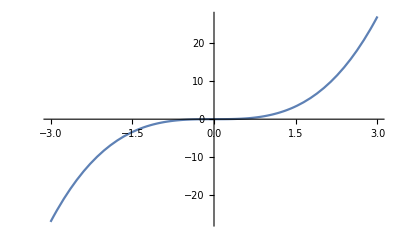

```mathematica
(*Hons 1st Year*)
(*Chapter 1,2*)
(*Major and Non Major*)
 Plot[x^3,{x,-3,3}]
```

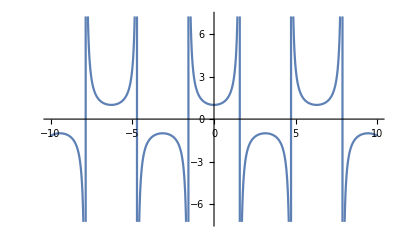

Pl0t[x^2,{x,-6,6}]

```mathematica
Plot[Sec[x],{x,-10,10}]
```

TraditionalForm[expr]

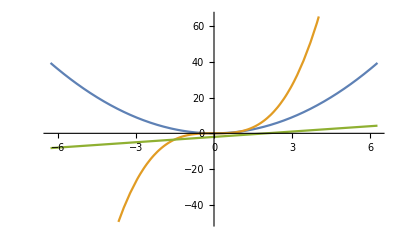

```mathematica
Plot[{x^2,x^3,x-2},{x,-2π ,2π}]
```

```mathematica
?Fibonacci
```

Fibonacci[n] gives the Fibonacci number F_n. 
Fibonacci[n,x] gives the Fibonacci polynomial F_n(x).

```mathematica
?Factorial
```

n! gives the factorial of n.

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
FindRoot[Sin[x]==x^2-1,{x,-1}]
```

{x→-0.636733}

```mathematica
9!
```

362880

```mathematica
?Solve
```

Solve[expr,vars] attempts to solve the system expr of equations or inequalities for the variables vars. 
Solve[expr,vars,dom] solves over the domain dom. Common choices of dom are Reals, Integers, and Complexes.

```mathematica
Solve[{2x+y==5, 3x+2y==6},{x,y}]
```

{{x→4,y→-3}}

```mathematica
?Prime
```

Prime[n] gives the n^th prime number.

```mathematica
Prime[40]
```

173

```mathematica
?Plot
```

Plot[
StyleBox["f", "TI"], {
StyleBox["x", "TI"], SubscriptBox[
StyleBox["x", "TI"], 
StyleBox["min", "TI"]], SubscriptBox[
StyleBox["x", "TI"], 
StyleBox["max", "TI"]]}] generates a plot of 
StyleBox["f", "TI"] as a function of 
StyleBox["x", "TI"] from SubscriptBox[
StyleBox["x", "TI"], 
StyleBox["min", "TI"]] to SubscriptBox[
StyleBox["x", "TI"], 
StyleBox["max", "TI"]]. \nPlot[{SubscriptBox[
StyleBox["f", "TI"], 
StyleBox["1", "TR"]], SubscriptBox[
StyleBox["f", "TI"], 
StyleBox["2", "TR"]], 
StyleBox["…", "TR"]}, {
StyleBox["x", "TI"], SubscriptBox[
StyleBox["x", "TI"], 
StyleBox["min", "TI"]], SubscriptBox[
StyleBox["x", "TI"], 
StyleBox["max", "TI"]]}] plots several functions SubscriptBox[
StyleBox["f", "TI"], 
StyleBox["i", "TI"]].

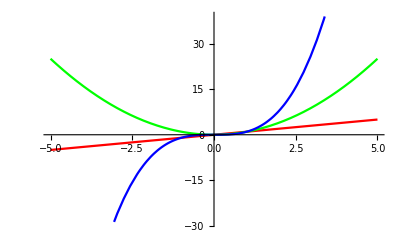

```mathematica
Plot[{x,x^2,x^3},{x,-5,5},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]}]
```

```mathematica
NSolve[X^2-X+1==0]
```

{{X→0.5-0.866025 ⅈ},{X→0.5+0.866025 ⅈ}}

```mathematica
Solve[X^2-X+1==0]
```

{{X→(-1)^(1/3)},{X→-(-1)^(2/3)}}

```mathematica
N[GoldenRatio]
```

1.61803

```mathematica
N[π,55]
```

3.141592653589793238462643383279502884197169399375105821

```mathematica
N[EulerGamma,20]
```

0.57721566490153286061

```mathematica
N[Catalan,30]
```

0.915965594177219015054603514932

```mathematica
Fibonacci[7]
```

13

```mathematica
Random[Real,{π,2π},16]
```

5.323236473549414

```mathematica
p=Random[Integer,{10000,99999}]
```

47644

```mathematica
q=Random[Integer,{1000,9999}]
```

7028

```mathematica
lcm=LCM[p,q]
```

83710508

```mathematica
gcd=GCD[p,q]
```

4

```mathematica
gcd*lcm==p*q
```

True

```mathematica
154.AREA OF A TR
```

```mathematica
s=(a+b+c)/2;
A[a_,b_,c_]=√(s*(s-a)*(s-b)*(s-c))
A[3,4,5]
A[6,7,9]A[4,5,6]
```

1/(√2)(√((a+b+c) (-a+1/2 (a+b+c)) (-b+1/2 (a+b+c)) (-c+1/2 (a+b+c))))

6

15 √(385/2)

1/(√2)(√((a+b+c) (-a+1/2 (a+b+c)) (-b+1/2 (a+b+c)) (-c+1/2 (a+b+c))))

6

2 √110

```mathematica
A[5,9,12]
```

4 √26

```mathematica
FactorInteger[6]
```

{{2,1},{3,1}}

```mathematica
d[x1_,y1_,x2_,y2_]=√((x2-x1)^2+(y2-y1)^2);
d[3,5,-1,-2]
```

√65

```mathematica
d[x1_,y1_,x2_,y2_]=√((x2-x1)^2+(y2-y1)^2);
d[4,6,-2,5]
```

√37

d[6,5,-4,-25]

```mathematica
(*Q174.find the sum of the series1.2+2.3+3.4+---*)
```

nth term = n (n + 1)

```mathematica
Sum[i*(i+1),{i,1,n}]
```

1/3 n (1+n) (2+n)

```mathematica
Q138.Using do loop, while loop and for loop find 10!*)
```

```mathematica
fact=1;
n=10;
Do[fact=fact*k,{k,n}]
fact
```

3628800

```mathematica
fact=1;
n=10;
While[n>0, fact=fact*n;n--]
fact
```

3628800

```mathematica
For[fact=1;n=1,n≤10,n++,fact=n*fact]
fact
```

3628800

```mathematica
f[x_]:=ⅇ^x/;x>2
f[x_]:=1-x^2/;x≤2
f[3]
```

ⅇ^3

```mathematica
f[1]
```

0

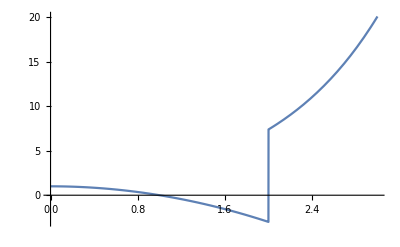

```mathematica
Plot[f[x],{x,0,3}]
```

```mathematica
96.
```

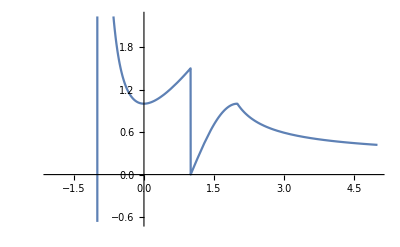

```mathematica
g[x_]:=(1-x^3)/(1-x^2)/;x<1
g[x_]:=Sin[(π*(x-1))/2]/;1≤x≤2
g[x_]:=1/Log[E(x-1)]/;x>2
Plot[g[x],{x,-2,5}]
```

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
(*Q-41.Write MathematicccaNotation to find all the numbers less than 1000 which are both prime and fibonacce.*)
```

```mathematica
k=1;set1={};
While[Fibonacci[k]≤1000,
set1=Append[set1,Fibonacci[k]];k++]
k=1;set2={};
While[Prime[k]≤1000,set2=Append[set2,Prime[k]];k++]
Intersection[set1,set2]
```

{2,3,5,13,89,233}

```mathematica
(*Q-66.Using the standard TableForm CONSTRUCT a table having 3 columns.The first column lists the consecutive integers 1 through 5 and the second and third columns are thier square roots and cube roots respectively.*)
```

```mathematica
lst=Table[{k,N[√k],N[k^(1/3)]},{k,1,5}];
TableForm[lst]
```

1 | 1. | 1.
2 | 1.41421 | 1.25992
3 | 1.73205 | 1.44225
4 | 2. | 1.5874
5 | 2.23607 | 1.70998

```mathematica
Transpose[{{1,1.,1.},{2,1.4142135623730951,1.2599210498948732},{3,1.7320508075688772,1.4422495703074083},{4,2.,1.5874010519681994},{5,2.23606797749979,1.7099759466766968}}]
```

{{1,2,3,4,5},{1.,1.41421,1.73205,2.,2.23607},{1.,1.25992,1.44225,1.5874,1.70998}}

```mathematica
(*75 *)
```

```mathematica
L1=Table[k,{k,1,100}];
L2=Table[7k,{k,1,100/7}];
L3=Complement[L1,L2];L4=Partition[L3,7];
TableForm[L4,TableAlignments->Left]
```

1 | 2 | 3 | 4 | 5 | 6 | 8
9 | 10 | 11 | 12 | 13 | 15 | 16
17 | 18 | 19 | 20 | 22 | 23 | 24
25 | 26 | 27 | 29 | 30 | 31 | 32
33 | 34 | 36 | 37 | 38 | 39 | 40
41 | 43 | 44 | 45 | 46 | 47 | 48
50 | 51 | 52 | 53 | 54 | 55 | 57
58 | 59 | 60 | 61 | 62 | 64 | 65
66 | 67 | 68 | 69 | 71 | 72 | 73
74 | 75 | 76 | 78 | 79 | 80 | 81
82 | 83 | 85 | 86 | 87 | 88 | 89
90 | 92 | 93 | 94 | 95 | 96 | 97

```mathematica
(*Q 144 Demorgan's rule:*)
```

```mathematica
LogicalExpand[!(p&&q)]==LogicalExpand[!p||!q]
```

True

```mathematica
LogicalExpand[!(p||q)]==LogicalExpand[!p&&!q]
```

True

```mathematica
(*q_111- Write Mathematica code to print all numbers from 1 to 50 which are not multiples of 2, 3 or 5*)
 L1=Table[k,{k,1,50}];
L2 = Table[2*k,{k,1,50/2}];
L3 = Table[3*k,{k,1,50/3}];
L4 = Table[5*k,{k,1,50/5}];
L5 = Complement[L1,L2,L3,L4];
L6 = Partition[L5,3];
TableForm[L6,TableAlignments->Left]
```

1 | 7 | 11
13 | 17 | 19
23 | 29 | 31
37 | 41 | 43

```mathematica
(*Ex-112] Using Mathematica to find the integers from 1 to 100 which are not multiple of 2,3,5*)
L1=Table[k,{k,1,100}];
L2 = Table[2*k,{k,1,100/2}];
L3 = Table[3*k,{k,1,100/3}];
L4 = Table[5*k,{k,1,100/5}];
L5 = Complement[L1,L2,L3,L4];
L6 = Partition[L5,4];
TableForm[L6,TableAlignments->Left]
```

1 | 7 | 11 | 13
17 | 19 | 23 | 29
31 | 37 | 41 | 43
47 | 49 | 53 | 59
61 | 67 | 71 | 73
77 | 79 | 83 | 89

Syntax::tsntxi: " (*q_ 111 - «1»," is incomplete; more input is needed.""

```mathematica
(*q114-Write Mathematica Command to construct a table showing the radian equivalents of angle from 0° to 45° in increment of 5*)
first=Table[{deg,N[deg Degree]},{deg,0,45,5}];
TableForm[first,TableDirections->Column,TableHeadings->{None,{"Degree","Radian"}}]
```

Degree | Radian
0 | 0.
5 | 0.0872665
10 | 0.174533
15 | 0.261799
20 | 0.349066
25 | 0.436332
30 | 0.523599
35 | 0.610865
40 | 0.698132
45 | 0.785398

```mathematica
(*q115-Write Mathematica Command to construct a table showing the radian equivalents of angle from 0° to 180° in increment of 15°*)
first=Table[{deg,N[deg Degree]},{deg,0,180,15}];
TableForm[first,TableDirections->Column,TableHeadings->{None,{"Degree","Radian"}}]
```

Degree | Radian
0 | 0.
15 | 0.261799
30 | 0.523599
45 | 0.785398
60 | 1.0472
75 | 1.309
90 | 1.5708
105 | 1.8326
120 | 2.0944
135 | 2.35619
150 | 2.61799
165 | 2.87979
180 | 3.14159

```mathematica
(*Ex-121 If C represents the temperature in degree Celcius, its corresponding Farenheit temparature is f = 1.4 C+32 degrees.Construct a labeled table showing,horizontally, the Farenheit equivalents of Celsius temparatures from 1 to 10 degree in the increments of 1 degree*)
```

```mathematica
f= 1.4*c+32
first=Table[{c,PaddedForm[N[f],{3,1}]},{c,1,10}];
TableForm[first,TableDirections->Row,TableHeadings->{None,{"Celcius","Farenhiet"}},TableAlignments->Center]
```

32+1.4 c

Celcius | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
Farenhiet |  33.4 |  34.8 |  36.2 |  37.6 |  39.0 |  40.4 |  41.8 |  43.2 |  44.6 |  46.0